```mathematica
Needs["ErrorBarPlots`"]
```

# Labor - Ex1 - Temperatur

## Messung

Temperatur und Volumen zu Raumtemperatur

Alle 0 Werte bei Raumtemperatur.

```mathematica
dataT0 = 0
```

0

```mathematica
dataT0Fehler = 0
```

0

```mathematica
dataV0 = 0
```

0

```mathematica
dataV0Fehler = 0
```

0

```mathematica
dataR0 = 0
```

0

```mathematica
dataR0Fehler = 0
```

0

Volumen (Gasthermometer), Spannung (Thermoelement), R - NTC, R - PTC

```mathematica
dataTemAll = ({{"N", "Temperatur", "Diff-Temp", "Volumen", "Spannung", "R-NTC", "R-PTC"}, {1, 0, 0, 0, 0, 0, 0}, {2, 0, 0, 0, 0, 0, 0}, {3, 0, 0, 0, 0, 0, 0}, {4, 0, 0, 0, 0, 0, 0}, {5, 0, 0, 0, 0, 0, 0}, {6, 0, 0, 0, 0, 0, 0}, {7, 0, 0, 0, 0, 0, 0}, {8, 0, 0, 0, 0, 0, 0}, {9, 0, 0, 0, 0, 0, 0}, {10, 0, 0, 0, 0, 0, 0}})
```

{{N,Temperatur,Diff-Temp,Volumen,Spannung,R-NTC,R-PTC},{1,0,0,0,0,0,0},{2,0,0,0,0,0,0},{3,0,0,0,0,0,0},{4,0,0,0,0,0,0},{5,0,0,0,0,0,0},{6,0,0,0,0,0,0},{7,0,0,0,0,0,0},{8,0,0,0,0,0,0},{9,0,0,0,0,0,0},{10,0,0,0,0,0,0}}

```mathematica
dataTemFehler = 0
```

0

```mathematica
dataDiffTempFehler = 0
```

0

```mathematica
dataVolFehler = dataV0Fehler
```

0

```mathematica
dataSpannungFehler = 0
```

0

```mathematica
dataWidFehler = 0
```

0

## Rechnung

Diagramm Volumen

```mathematica
dataVolPlotError=Table[{dataTemAll[[i,2]],dataTemAll[[i,4]],ErrorBar[dataTemFehler,dataVolFehler]},{i,2,11}]
```

{{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]}}

```mathematica
dataVolPlot = Table[{dataTemAll[[i,2]],dataTemAll[[i,4]]},{i,2,11}]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

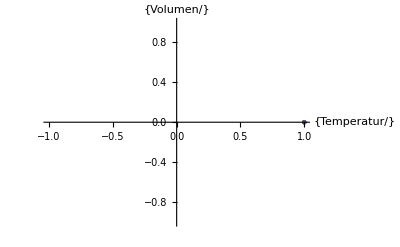

```mathematica
Show[ListLinePlot[dataVolPlot],ErrorListPlot[dataVolPlotError], AxesLabel-> {{"Temperatur/"},{"Volumen/"}}]
```

Absolute Temperatur

```mathematica
F_AbsTemp[V_] := {(dataT0*V)/dataV0,Abs[V/dataV0]*dataT0Fehler+Abs[dataT0/dataV0]*dataVolFehler+Abs[(dataT0*V)/dataV0^2]*dataV0Fehler}
```

```mathematica
F_AbsTemp[Table[dataTemAll[[i,2]],{i,2,11}]]
```

F_AbsTemp[{0,0,0,0,0,0,0,0,0,0}]

Spannung, Thermokraft des Thermoelements

```mathematica
dataSpannungPlot = Table[{dataTemAll[[i,3]],dataTemAll[[i,5]]},{i,2,11}]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
dataSpannungPlotError=Table[{dataTemAll[[i,3]],dataTemAll[[i,5]],ErrorBar[dataDiffTempFehler,dataSpannungFehler]},{i,2,11}]
```

{{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]}}

```mathematica
SpannungFit= LinearModelFit[dataSpannungPlot,x,x]
```

FittedModel[0.]

```mathematica
SpannungFitPara = SpannungFit["ParameterTable"]
```

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

| Estimate | Standard Error | t Statistic | P-Value
1 | 0. | 0. | ComplexInfinity | 0.

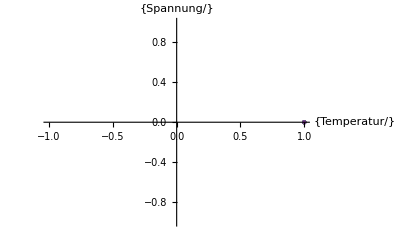

```mathematica
Show[ListLinePlot[dataSpannungPlot],ErrorListPlot[dataSpannungPlotError],AxesLabel-> {{"Temperatur/"},{"Spannung/"}}]
```

NTC Widerstand, R∞, ΔE

```mathematica
dataNtcPlot = Table[{1/dataTemAll[[i,2]],dataTemAll[[i,6]]},{i,2,11}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

{{ComplexInfinity,0},{ComplexInfinity,0},{ComplexInfinity,0},{ComplexInfinity,0},{ComplexInfinity,0},{ComplexInfinity,0},{ComplexInfinity,0},{ComplexInfinity,0},{ComplexInfinity,0},{ComplexInfinity,0}}

PTC Widerstand, α

```mathematica
dataPtcPlot = Table[{dataTemAll[[i,2]],dataTemAll[[i,7]]},{i,2,11}]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
dataPtcPlotError=Table[{dataTemAll[[i,2]],dataTemAll[[i,7]],ErrorBar[dataTemFehler,dataWidFehler]},{i,2,11}]
```

{{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]},{0,0,ErrorBar[0,0]}}

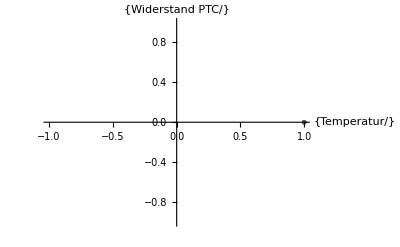

```mathematica
Show[ListLinePlot[dataPtcPlot],ErrorListPlot[dataPtcPlotError],AxesLabel-> {{"Temperatur/"},{"Widerstand PTC/"}}]
```

```mathematica
PTCFit= LinearModelFit[dataPtcPlot,x,x]
```

FittedModel[0.]

```mathematica
PTCFitPara = PTCFit["ParameterTable"]
```

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

| Estimate | Standard Error | t Statistic | P-Value
1 | 0. | 0. | ComplexInfinity | 0.

Nachdem die Formel R(T) = R0*(1+αT) = R0 + R0*α*T lautet -> α*R0 = k -> α = k/R0